## LeNet and MNIST data

```mathematica
mnistTrain=ResourceData["MNIST","TrainingData"];
mnistTest=ResourceData["MNIST","TestData"];
```

```mathematica
ResourceSearch["mnist"]
```

```mathematica
lenetModel=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

```mathematica
Information[lenetModel]
```

Net Information

```mathematica
Information[lenetModel,"SummaryGraphic"]
```

-Graphics-

```mathematica
NetMeasurements[lenetModel,mnistTest,"Accuracy"]
```

0.9848

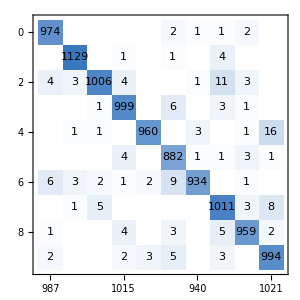
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[lenetModel,mnistTest,"ConfusionMatrixPlot"]
```

## Using the trained model

```mathematica
img=Import[NotebookDirectory[]<>"data/4738-v3.png"];
img=ImageCrop[ImageRotate[img,Pi/2]];
```

```mathematica
img
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/4738-v3-fixed.png",img]
```

/home/jam/Kuweta/mma_lessons/code/pics/4738-v3-fixed.png

```mathematica
img=Import[NotebookDirectory[]<>"pics/4738-v3-fixed.png"]
```

-Graphics-

```mathematica
d1=ImageResize[ImageCrop[img,{28*11.5,28*11.5},Right],{28,28}]
```

-Graphics-

```mathematica
y=50;ds=270; dw=11;
digits=Table[ImageResize[ImageTrim[img,{{x ds,y},{x ds+28dw,y+28 dw}}],{28,28}],{x,0,3,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Rasterize[digits]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"pics/4738-v3-digits.png",Rasterize[digits]]
```

/home/jam/Kuweta/mma_lessons/code/pics/4738-v3-digits.png

```mathematica
lenetModel[digits]
```

{5,7,3,8}

```mathematica
capsnetModel=NetModel["CapsNet Trained on MNIST Data"]
```

NetGraph[<8>, <12>]

```mathematica
Information[capsnetModel]
```

Net Information

```mathematica
capsnetModel[digits]
```

<|Classification→{1,7,3,8},Reconstruction→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}|>